# sistemas de equações diferenciais ordinárias de primeira ordem, autónomas

## aula online - segunda, dia 16 de novembro

## exemplo #1

```mathematica
Clear[eq01,eq02,jacX];
eq01[x_,y_]=-1-x+4 y-4 y^2;
eq02[x_,y_]=4 x+3 y-2 y^2;
```

```mathematica
jacX[{x_,y_}]=({{D[eq01[x,y],x], D[eq01[x,y],y]}, {D[eq02[x,y],x], D[eq02[x,y],y]}});
Print["matriz jacobiana do sistema = ",MatrixForm[jacX[{x,y}]]];
```

matriz jacobiana do sistema = (-1 | 4-8 y
4 | 3-4 y)

```mathematica
zeros01={x,y}/.NSolve[{eq01[x,y]==0,eq02[x,y]==0},{x,y}];
Print["soluções de tipo constante = ",zeros01];
```

soluções de tipo constante = {{-0.281136,0.765111},{-0.175654,0.290444}}

#### primeira solução de tipo constante

```mathematica
Print["solução constante = ",Part[zeros01,1]];
matA01=jacX[Part[zeros01,1]];
Print["matriz jacobiana do sistema na solução constante = ",MatrixForm[matA01]];
Print["valores próprios da matriz jacobiana calculada na solução constante = ",Eigenvalues[matA01]];
```

solução constante = {-0.281136,0.765111}

matriz jacobiana do sistema na solução constante = (-1 | -2.12089
4 | -0.0604449)

valores próprios da matriz jacobiana calculada na solução constante = {-0.530222+2.87452 ⅈ,-0.530222-2.87452 ⅈ}

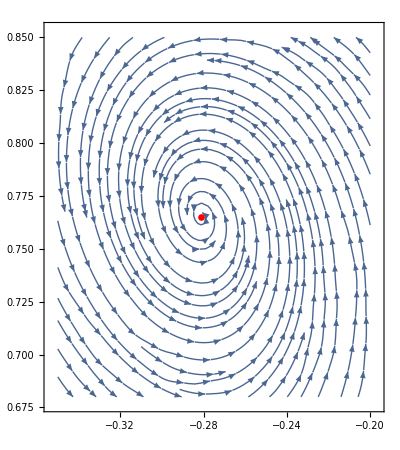

```mathematica
StreamPlot[{eq01[x,y],eq02[x,y]},{x,-0.35,-0.2},{y,0.68,0.85},Epilog->{Red,PointSize[0.012],Point[Part[zeros01,1]]},AspectRatio->Automatic,ImageSize->400]
```

#### segunda solução de tipo constante

```mathematica
Print["solução constante = ",Part[zeros01,2]];
matA02=jacX[Part[zeros01,2]];
Print["matriz jacobiana do sistema na solução constante = ",MatrixForm[matA02]];
Print["valores próprios da matriz jacobiana calculada na solução constante = ",Eigenvalues[matA02]];
```

solução constante = {-0.175654,0.290444}

matriz jacobiana do sistema na solução constante = (-1 | 1.67645
4 | 1.83822)

valores próprios da matriz jacobiana calculada na solução constante = {3.37202,-2.5338}

```mathematica
{{vectU,vectV}}=Drop[Eigensystem[matA02],1];
```

```mathematica
Clear[X,Y];
{{X[t_,{xo_,yo_}],Y[t_,{xo_,yo_}]}}=Expand[{x[t],y[t]}/.DSolve[{
x'[t]==Part[matA02,1,1]*x[t]+Part[matA02,1,2]*y[t],
y'[t]==Part[matA02,2,1]*x[t]+Part[matA02,2,2]*y[t],x[0]==xo,y[0]==yo},{x[t],y[t]},t]];
```

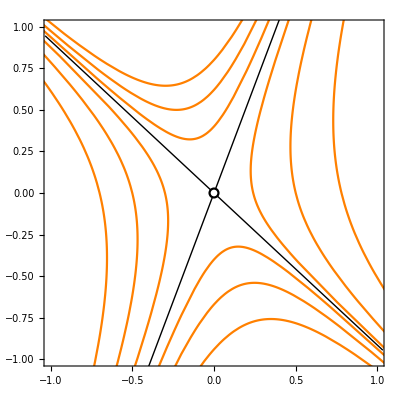

```mathematica
Clear[curvas01,curvas02];
curvas01={{X[t,-{0.5,0}],Y[t,-{0.5,0}]},{X[t,-{0.3,0}],Y[t,-{0.3,0}]},{X[t,-{0.7,0}],Y[t,-{0.7,0}]}};
curvas02={{X[t,{0,0.4}],Y[t,{0,0.4}]},{X[t,{0,0.62}],Y[t,{0,0.62}]},{X[t,{0,0.8}],Y[t,{0,0.8}]}};
curvas03={{X[t,{0.24,0}],Y[t,{0.24,0}]},{X[t,{0.5,0}],Y[t,{0.5,0}]},{X[t,{0.78,0}],Y[t,{0.78,0}]}};
curvas04={{X[t,{0,-0.4}],Y[t,{0,-0.4}]},{X[t,{0,-0.67}],Y[t,{0,-0.67}]},{X[t,{0,-0.94}],Y[t,{0,-0.94}]}};ParametricPlot[{curvas01,curvas02,curvas03,curvas04},{t,-4,4},PlotStyle->Orange,AspectRatio->Automatic,PlotRange->{{-1,1},{-1,1}},Frame->True,Epilog->{{Line[{-1.2vectU,1.2vectU}],Line[{-1.4vectV,1.4vectV}]},{PointSize[0.02],Black,Point[{0,0}]},{PointSize[0.012],White,Point[{0,0}]}}]
```

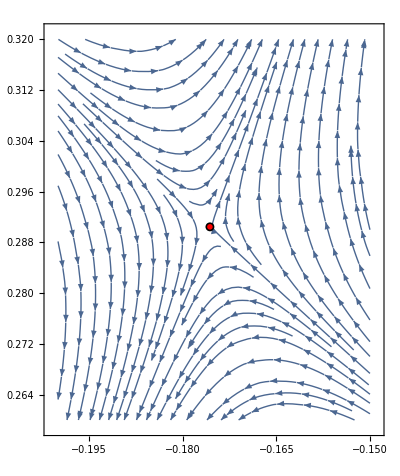

```mathematica
StreamPlot[{eq01[x,y],eq02[x,y]},{x,-0.2,-0.15},{y,0.26,0.32},Epilog->{{Black,PointSize[0.016],Point[Part[zeros01,2]]},{Red,PointSize[0.01],Point[Part[zeros01,2]]}},AspectRatio->Automatic,ImageSize->400]
```

#### juntando os dois

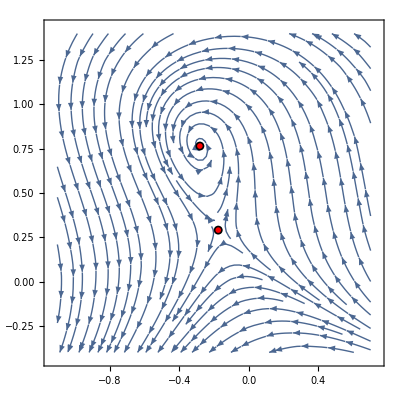

```mathematica
StreamPlot[{eq01[x,y],eq02[x,y]},{x,-1.1,0.7},{y,-0.4,1.4},Epilog->{{Black,PointSize[0.016],Point[zeros01]},{Red,PointSize[0.01],Point[zeros01]}},AspectRatio->Automatic,ImageSize->400]
```

## exemplo #2

```mathematica
Clear[eq01,eq02,jacX];
eq01[x_,y_]=-1-x-x^2+3 y+2 y^2;
eq02[x_,y_]=1+x-4 x^2+3 y^2;
```

```mathematica
jacX[{x_,y_}]=({{D[eq01[x,y],x], D[eq01[x,y],y]}, {D[eq02[x,y],x], D[eq02[x,y],y]}});
Print["matriz jacobiana do sistema = ",MatrixForm[jacX[{x,y}]]];
```

matriz jacobiana do sistema = (-1-2 x | 3+4 y
1-8 x | 6 y)

```mathematica
zeros02={x,y}/.NSolve[{eq01[x,y]==0,eq02[x,y]==0},{x,y}];
Print["soluções de tipo constante = ",zeros02];
```

soluções de tipo constante = {{-1.72163,-2.04757},{3.27741,-3.59111},{0.868611,0.618959},{-0.424393,0.219721}}

#### primeira solução de tipo constante

```mathematica
Print["solução constante = ",Part[zeros02,1]];
matA01=jacX[Part[zeros02,1]];
Print["matriz jacobiana do sistema na solução constante = ",MatrixForm[matA01]];
Print["valores próprios da matriz jacobiana calculada na solução constante = ",Eigenvalues[matA01]];
```

solução constante = {-1.72163,-2.04757}

matriz jacobiana do sistema na solução constante = (2.44325 | -5.19028
14.773 | -12.2854)

valores próprios da matriz jacobiana calculada na solução constante = {-4.92108+4.73736 ⅈ,-4.92108-4.73736 ⅈ}

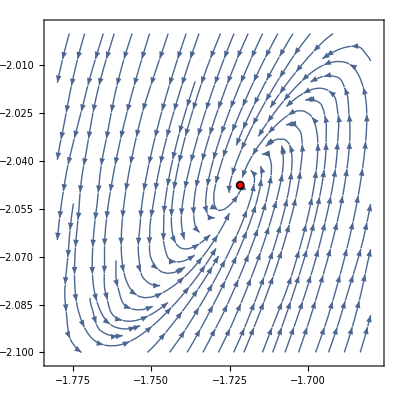

```mathematica
StreamPlot[{eq01[x,y],eq02[x,y]},{x,-1.78,-1.68},{y,-2.1,-2.0},Epilog->{{Black,PointSize[0.016],Point[zeros02]},{Red,PointSize[0.01],Point[zeros02]}},AspectRatio->Automatic,ImageSize->400]
```

#### segunda solução de tipo constante

```mathematica
Print["solução constante = ",Part[zeros02,2]];
matA02=jacX[Part[zeros02,2]];
Print["matriz jacobiana do sistema na solução constante = ",MatrixForm[matA02]];
Print["valores próprios da matriz jacobiana calculada na solução constante = ",Eigenvalues[matA02]];
```

solução constante = {3.27741,-3.59111}

matriz jacobiana do sistema na solução constante = (-7.55482 | -11.3644
-25.2193 | -21.5467)

valores próprios da matriz jacobiana calculada na solução constante = {-32.8686,3.76717}

```mathematica
{{vectU,vectV}}=Drop[Eigensystem[matA02],1];
```

```mathematica
Clear[X,Y];
{{X[t_,{xo_,yo_}],Y[t_,{xo_,yo_}]}}=Expand[{x[t],y[t]}/.DSolve[{
x'[t]==Part[matA02,1,1]*x[t]+Part[matA02,1,2]*y[t],
y'[t]==Part[matA02,2,1]*x[t]+Part[matA02,2,2]*y[t],x[0]==xo,y[0]==yo},{x[t],y[t]},t]];
```

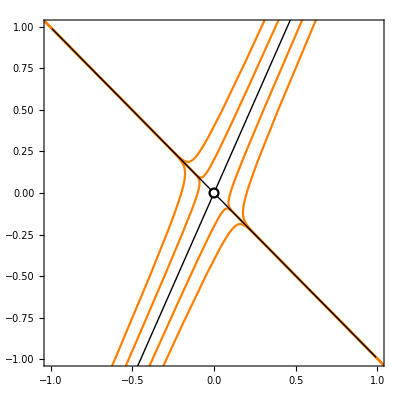

```mathematica
Clear[curvas01,curvas02];
curvas01={{X[t,{0.1,0}],Y[t,{0.1,0}]},{X[t,-{0.1,0}],Y[t,-{0.1,0}]},{X[t,{0.2,0}],Y[t,{0.2,0}]},{X[t,-{0.2,0}],Y[t,-{0.2,0}]}};
curvas02={{X[t,{0,0.2}],Y[t,{0,0.2}]},{X[t,-{0,0.2}],Y[t,-{0,0.2}]},{X[t,{0,0.4}],Y[t,{0,0.4}]},{X[t,-{0,0.4}],Y[t,-{0,0.4}]}};
ParametricPlot[{curvas01,curvas02},{t,-0.1,0.8},PlotStyle->Orange,AspectRatio->Automatic,PlotRange->{{-1,1},{-1,1}},Frame->True,Epilog->{{Line[{-1.2vectU,1.2vectU}],Line[{-1.4vectV,1.4vectV}]},{PointSize[0.02],Black,Point[{0,0}]},{PointSize[0.012],White,Point[{0,0}]}}]
```

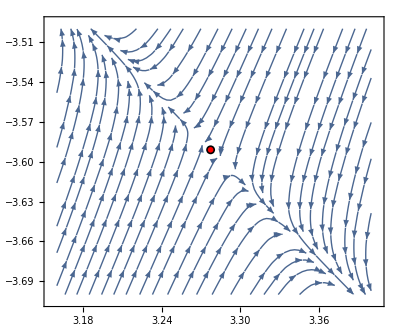

```mathematica
StreamPlot[{eq01[x,y],eq02[x,y]},{x,3.16,3.4},{y,-3.7,-3.5},Epilog->{{Black,PointSize[0.016],Point[Part[zeros02,2]]},{Red,PointSize[0.01],Point[Part[zeros02,2]]}},AspectRatio->Automatic,ImageSize->400]
```

#### terceira solução de tipo constante

```mathematica
Print["solução constante = ",Part[zeros02,3]];
matA03=jacX[Part[zeros02,3]];
Print["matriz jacobiana do sistema na solução constante = ",MatrixForm[matA03]];
Print["valores próprios da matriz jacobiana calculada na solução constante = ",Eigenvalues[matA03]];
```

solução constante = {0.868611,0.618959}

matriz jacobiana do sistema na solução constante = (-2.73722 | 5.47584
-5.94889 | 3.71375)

valores próprios da matriz jacobiana calculada na solução constante = {0.488265+4.70865 ⅈ,0.488265-4.70865 ⅈ}

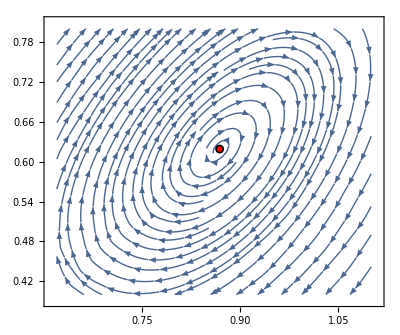

```mathematica
StreamPlot[{eq01[x,y],eq02[x,y]},{x,0.62,1.1},{y,0.4,0.8},Epilog->{{Black,PointSize[0.016],Point[Part[zeros02,3]]},{Red,PointSize[0.01],Point[Part[zeros02,3]]}},AspectRatio->Automatic,ImageSize->400]
```

#### quarta solução de tipo constante

```mathematica
Print["solução constante = ",Part[zeros02,4]];
matA04=jacX[Part[zeros02,4]];
Print["matriz jacobiana do sistema na solução constante = ",MatrixForm[matA04]];
Print["valores próprios da matriz jacobiana calculada na solução constante = ",Eigenvalues[matA04]];
```

solução constante = {-0.424393,0.219721}

matriz jacobiana do sistema na solução constante = (-0.151214 | 3.87888
4.39515 | 1.31832)

valores próprios da matriz jacobiana calculada na solução constante = {4.77738,-3.61027}

```mathematica
{{vectU,vectV}}=Drop[Eigensystem[matA04],1];
```

```mathematica
Clear[X,Y];
{{X[t_,{xo_,yo_}],Y[t_,{xo_,yo_}]}}=Expand[{x[t],y[t]}/.DSolve[{
x'[t]==Part[matA04,1,1]*x[t]+Part[matA04,1,2]*y[t],
y'[t]==Part[matA04,2,1]*x[t]+Part[matA04,2,2]*y[t],x[0]==xo,y[0]==yo},{x[t],y[t]},t]];
```

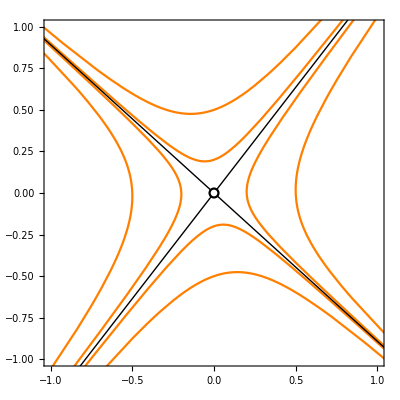

```mathematica
Clear[curvas01,curvas02];
curvas01={{X[t,{0.2,0}],Y[t,{0.2,0}]},{X[t,-{0.2,0}],Y[t,-{0.2,0}]},{X[t,{0.5,0}],Y[t,{0.5,0}]},{X[t,-{0.5,0}],Y[t,-{0.5,0}]}};
curvas02={{X[t,{0,0.2}],Y[t,{0,0.2}]},{X[t,-{0,0.2}],Y[t,-{0,0.2}]},{X[t,{0,0.5}],Y[t,{0,0.5}]},{X[t,-{0,0.5}],Y[t,-{0,0.5}]}};
ParametricPlot[{curvas01,curvas02},{t,-1.1,1.8},PlotStyle->Orange,AspectRatio->Automatic,PlotRange->{{-1,1},{-1,1}},Frame->True,Epilog->{{Line[{-1.5vectU,1.5vectU}],Line[{-1.5vectV,1.5vectV}]},{PointSize[0.02],Black,Point[{0,0}]},{PointSize[0.012],White,Point[{0,0}]}}]
```

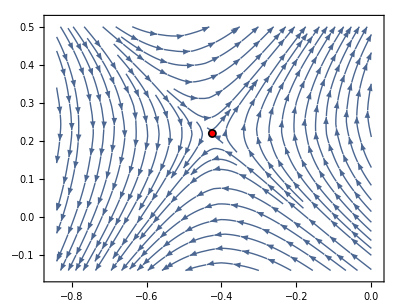

```mathematica
StreamPlot[{eq01[x,y],eq02[x,y]},{x,-0.84,0},{y,-0.14,0.5},Epilog->{{Black,PointSize[0.016],Point[Part[zeros02,4]]},{Red,PointSize[0.01],Point[Part[zeros02,4]]}},AspectRatio->Automatic,ImageSize->400]
```

#### juntando todos

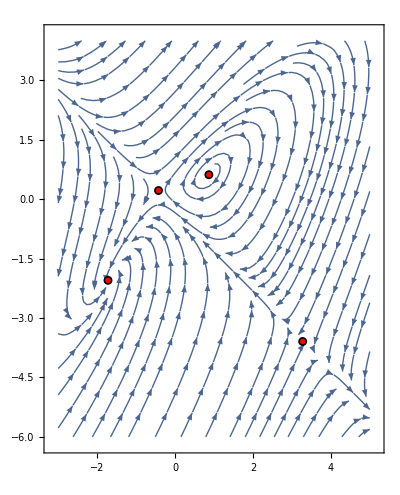

```mathematica
StreamPlot[{eq01[x,y],eq02[x,y]},{x,-3,5},{y,-6,4},Epilog->{{Black,PointSize[0.016],Point[zeros02]},{Red,PointSize[0.01],Point[zeros02]}},AspectRatio->Automatic,ImageSize->400]
```